# A Computational Sustainability Toolkit

## Lessons in Energy Monitoring and Application Building using the Wolfram Language

## Introduction

I hope that these materials provide students with an understanding of how to use computational technology and computational thinking in their pursuit of a more sustainable world. To that end, these materials provide :

*A series of lessons on how to specify, build and deploy software generally, and specifically with the Wolfram Language,

*An introduction to the concept of Computational Sustainability,

*the source code of an application that students, and their school communities, can use to track and hopefully manage their school' s energy consumption.

## A note on structure

This project is about much more than delivering the code for a software application.In addition to the code produced, it is meant to provide an introduction to the processs of software design and an introduction to the concept of computational sustainability.The introduction to the process of software design comes largely through the use of User Stories to specify the requested functionality.The introduction to Computational Sustainability comes through some of the background materials provided, as well as through the exercise of gathering and analyzing data.

For those not familiar with the concept, User Stories are a common method of defining requirements in the world of software development.The basic structure of a user story is to state who the user is, what the user needs to do, and why.In the context of these materials, I hope that pairing each incremental piece of code with a statement of the functional requirement that it satisfies will help to clarify the relationship between the two.

## For School Groups

Implementing a project to monitor a school' s energy consumption with this set of tools has only three prerequisites :

*a single individual willing to put in the required effort,

*a basic Wolfram Cloud account,

*the ability to record the values displayed on the school' s utility meters.

Schools will be able to achieve much more when students, teachers and administrators collaborate together on a project, but a single student will be able to get things started.

## For Interested Contributors

There are many ways that individuals can contribute to this project.Those interested in features that go beyond what has already been provided are welcome to submit feature requests, or better yet, to write out a user story that fully specifies the requested feature.Those with background in energy management, or other related fields, are encouraged to provide background materials within the context of a specific user story.Those with experience with the Wolfram Language are encouraged to provide code that satisfies the requirements spelled out in the user stories.Since this project is as much about an education on the process of software development, as it is about delivering an application, all new features will be delivered with accompanying user stories and background materials.

## Computational Sustainability

So, what is Computational Sustainability? On its website computational-sustainability.org the Institute for Computational Sustainability states:

Computational Sustainability is an interdisciplinary field that aims to apply techniques from computer science, information science, operations research, applied mathematics, and statistics for balancing environmental, economic, and societal needs for sustainable development. 

Focus: developing computational and mathematical models and methods for decision making concerning the management and allocation of resources in order to help solve some of the most challenging problems related to sustainability.

Computational Sustainability as a field extends far beyond energy consumption on school campuses, and at some point these materials may expand beyond that scope.At the moment, focusing on energy consumption in schools is the place to start because of the immediate relevance to students, and the ability of students to have some influence on the energy consumed in their schools.

## Section 1: A basic application for a single building

## Overview

In this section we will build a simple application that will allow students to track all of the energy consumption of a single building.  The first chapter provides the very basic building blocks required to build an application to record, save and plot daily kwh register readings from a single electric meter.  In the second chapter we will add the ability to manage additional commodities, as well as different data types, such as interval data.  We will also learn how to import data from a spreadsheet.  In the third chapter we tie the individual components from the first two chapters into an application that can track all of the energy consumed by a single building.

## Chapter 1: Recording Register Readings from an Electric Meter

## Background

In this chapter we will learn how to record, save and plot daily kwh register readings from a single electric meter.  We will learn the basics of plotting TimeSeries, and we will learn how to store information in a CloudExpression.  We will also create forms that can be used in a notebook, or through a browser,  to add new data to the CloudExpression, and create browser accessible visualizations so that information collected by the group can be shared.

### Register Readings

If students will be recording energy consumption directly from the face of the meter they will be recording register readings.

The values displayed on a typical electric or gas meter represent the total quantity of the commodity measured by the meter since it was installed.  The values start at zero when the meter is installed, and increment with each unit of the commodity measured.  In early meters the quantity measured was represented by dials that rotated as the commodity flowed through the meter.  In modern meters the quantity measured is typically displayed on an LCD.  With either display type there is a limit to the number of digits that can be displayed.  Once the maximum value is reached for all dials, or digits, the values roll over to zeros, and continue to increase from zero.

```mathematica
WebImageSearch["electric meter","Images",MaxItems->5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Take care to note the unit and direction of the register value you record.  Modern meters are capable of recording measurements for several units of measure in both directions.  There should be a unit of measure indicator as in the image below.  In addition to kilowatt hours you may see maximum kilowatts or kilovar hour units as well.  We will return to these measurements in a later user story.  If your meter is configured to measure energy in both direction you will see two different kilowatt hour register values, one for each direction.  The values may be distinguished by the sign of the values with positive values typically representing energy delivered by the utility to the customer, and negative values representing energy delivered by the customer to the utility.

### Time Series

```mathematica
TextSentences[WikipediaData["time series"]][[;;6]]
```

{A time series is a series of data points indexed (or listed or graphed) in time order.,Most commonly, a time series is a sequence taken at successive equally spaced points in time.,Thus it is a sequence of discrete-time data.,Examples of time series are heights of ocean tides, counts of sunspots, and the daily closing value of the Dow Jones Industrial Average.,Time series are very frequently plotted via line charts.,Time series are used in statistics, signal processing, pattern recognition, econometrics, mathematical finance, weather forecasting, earthquake prediction, electroencephalography, control engineering, astronomy, communications engineering, and largely in any domain of applied science and engineering which involves temporal measurements.}

Time series are core to this application both conceptually and from a code perspective.  The Wolfram Language has a rich set of functionality for performing calculations on and visualising time series. To fully take advantage of that functionality the data must be represented as a TimeSeries object.   As the documentation for the TimeSeries function clarifies the input necessary to create a TimeSeries object is a list of time-value pairs.  For reasons that will become clear when we cover storing data as CloudExpressions, I recommend that data be stored as a list of time-value pairs, instead of as a TimeSeries object.

## User Stories

### Create a list of daily kilowatt hour register readings

#### Story Details

As a participant in my school’s energy tracking initiative I want to create a list of daily kilowatt hour register readings running from 8 days ago to the day before yesterday.

#### Code Explanation

This first operation creates a List of time-value pairs named registerReadings.  Date-time values can be specified in a number of ways within the Wolfram Language but the DateObject provides the most robust means of specifying a date and time.  The value of each time-value pair could be specified as an Integer or Real, however  In this case using the QuantityMagnitude function allows us to assign kilowatt hour units to the value.

Note the date functions used to specify the date in the list below.  Typically you would specify a DateObject with a specific date, such as DateObject[{2019,11,7}].  In this case the relative dates will ensure that as you evaluate the code in this user story, and in subsequent stories within this chapter, you will have a continuous series of dates.  Following this chapter we will almost always use specific dates.

```mathematica
registerReadings={{DatePlus[Yesterday,-7],QuantityMagnitude[Quantity[0, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-6],QuantityMagnitude[Quantity[3, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-5],QuantityMagnitude[Quantity[10, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-4],QuantityMagnitude[Quantity[17, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-3],QuantityMagnitude[Quantity[25, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-2],QuantityMagnitude[Quantity[35, "Hours" "Kilowatts"]]},
{DatePlus[Yesterday,-1],QuantityMagnitude[Quantity[40, "Hours" "Kilowatts"]]}
}
```

{{Day: Mon 6 Jan 2020,0},{Day: Tue 7 Jan 2020,3},{Day: Wed 8 Jan 2020,10},{Day: Thu 9 Jan 2020,17},{Day: Fri 10 Jan 2020,25},{Day: Sat 11 Jan 2020,35},{Day: Sun 12 Jan 2020,40}}

This next operation creates a TimeSeries object named registerReadingsTimeSeries by using the registerReadings list from the prior operation as the input to the TimeSeries function.  The resulting TimeSeries object can be used in a number of TimeSeries operations from visualizations to calculations.

```mathematica
registerReadingsTimeSeries=TimeSeries[registerReadings]
```

TimeSeries[…]

### Create a plot of daily register readings

#### Story Details

As a participant in my school’s energy tracking initiative, I want to be able to plot a series of the daily register readings that my group has recorded for a single meter.

#### Background

Plotting time series data with time on the x axis and the values on the Y axis provides an intuitive means of exploring data.  While the difference between each register reading is often more interesting, as the difference is the consumption of the commodity between the two register readings, we will start with plotting the register readings themselves.

#### Code Explanation

Plotting TimeSeries data is as simple as applying the DateListPlot to a TimeSeries object.  While this simplest use of DateListPlot is informative, there is a rich set of options that can be used to add annotations, and style to your plots.

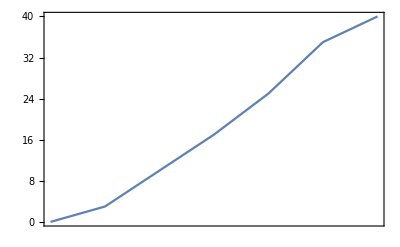

```mathematica
DateListPlot[registerReadingsTimeSeries]
```

A marker can be added for each data point by using PlotMarkers as an option.

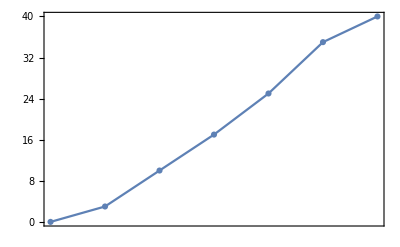

```mathematica
DateListPlot[
registerReadingsTimeSeries,
PlotMarkers->Automatic]
```

Each data point can be labeled with its value.

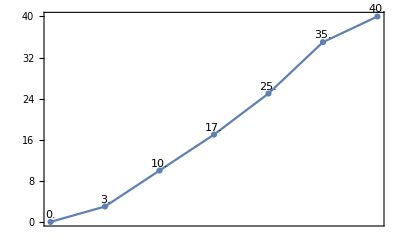

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

A number of  PlotTheme and PlotStyle options can be applied.

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Marketing"]
```

-Graphics-

### Calculate and plot daily consumption using daily register readings

#### Story Details

As a participant in my school’s energy savings initiative,  I want to be able to plot the daily usage captured by  register readings.

#### Code Explanation

For reference we start with one of the plots from the prior user story.

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

All that is needed to calculate, and plot, the daily consumption captured by the register readings is to apply the Differences function to the registerReadingsTimeSeries.  Differences calculates the difference between successive values in a TimeSeries, or List.

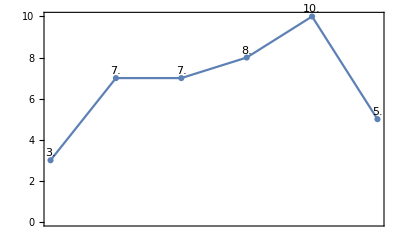

```mathematica
DateListPlot[
Differences[
registerReadingsTimeSeries],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

Another presentation option is a BarChart.

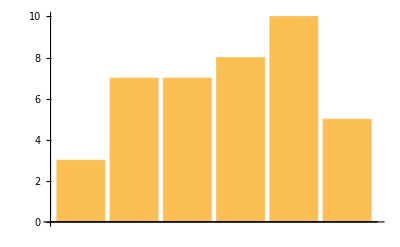

```mathematica
BarChart[Differences[registerReadingsTimeSeries]]
```

### Store Daily Register Reading Values in a CloudExpression

#### Story Details

As a participant in my school’s energy tracking initiative who has created a list of register readings for an electricity meter, I want to store those readings in a way that makes them easily available to other participants and applications.

#### Background Information

By storing data in a CloudExpression we can make that data available to other participants, or to applications that may make use of the data.  CloudExpressions can be protected with the Wolfram Language’s built in Permissions capability.  They can be made publicly accessible, they can be made accessible only to those with specific Wolfram IDs, or any user with a specific PermissionsKey.  It is also possible to define different levels of permissions for different PermissionsGroup or applications.

#### Code Explanation

This code takes advantage of the registerReadings list defined in the first user story.  Only the Owner is granted access to the CloudExpression if no other Permissions are set.

```mathematica
registerReadingsCloudExpression=CreateCloudExpression[registerReadings,"registerReadingsCloudExpression"]
```

CloudExpression[…]

This code returns the current permissions of the CloudExpression.

```mathematica
Options[registerReadingsCloudExpression,Permissions]
```

{Permissions→{Owner→{Read,Write,Execute}}}

This code provides public read access, while still providing the owner with complete Read, Write, Execute access.

```mathematica
SetPermissions[registerReadingsCloudExpression,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
Options[registerReadingsCloudExpression,Permissions]
```

```mathematica
DeleteCloudExpression["registerReadingsCloudExpression"]
```

### Graph daily register reads and daily usage from the contents of a Cloud Expression

#### Story Details

As a participant in my school’s energy tracking initiative I want to be able to plot the daily register readings and daily consumption from register readings stored in a CloudExpression.

#### Code Explanation

Any user with read permission for the CloudExpression can retrieve the contents of the CloudExpression with the Get function.  The code required to manipulate or plot the contents of a CloudExpression is identical to that used for data of the same structure in the local notebook.  Note the two methods of retrieving the CloudExpression used below.  In the first, Get evaluates a CloudExpression using the name specified in the second argument of CreateCloudExpression from the prior user story.  In the second, Get evaluates the name of the CloudExpression variable defined when the CloudExpression was defined.  This second method will only work using the same kernel session during which the CloudExpression was defined.

```mathematica
DateListPlot[TimeSeries[
Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

```mathematica
DateListPlot[Differences[TimeSeries[
Get[registerReadingsCloudExpression]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

### Create a Form for Register Reading Entry in Cloud Expression

#### Story Details

As a participant who is responsible for recording daily register readings, I would like to be able to use a form to enter the data, instead of manually typing the data in code.  I would like the form to assume that the date for the register reading is Yesterday.

### Code Explanation

The Wolfram Language provides the ability to create rich forms for data entry with relative ease.The FormPage function allows you to define a form which will invoke a function that operates on the contents entered into the form.  In this case the form asks for a daily register reading as an integer.  The function appends the entered value, along with yesterday’s date as a date-value pair to the list of date-value pairs that is the CloudExpression that contains register readings.

After you evaluate the code below, enter an integer value and press OK.  If you then evaluate the DateListPlot code below you will see the value that you entered appended to the plot.  Please note that since this form assume’s yesterday’s date, that it should only be used once a day for any meter.  In later stories we will explore ways to specify the date.

```mathematica
FormPage[
{"KWH"->"Integer"},
AppendTo[CloudExpression["registerReadingsCloudExpression"],{Yesterday,#KWH}]&,
AppearanceRules-><|"Title"->"Enter Yesterday's kWh Register Reading",
"Description"->"Enter an integer value"|>]
```

To verify that the form did add a new register reading to the CloudExpression, you can check with a DateListPlot.

```mathematica
DateListPlot[TimeSeries[Get[
CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

### Cloud Deploy a Form to Enable Data Entry on a Mobile Device

#### Story Details

As a participant responsible for recording daily register readings I would like to be able to enter the data on a mobile device so that I can record the register reading as I stand at the meter.

#### Code Explanation

A single Wolfram Language function allows you to deploy an enormous array of expressions to the cloud.  In this case, the deployed expression is a form that will append date - value pairs to the CloudExpression that holds your register readings.  As with the CloudExpression that contains the data, you will likely wish to use Permissions to limit access to the forms.  If you use Permissions, participants will need to log in to their Wolfram account to access the forms.  The Cloud Permissions Control Guide provides an overview of the available Permissions functions.

Without adding additional Permissions, only the user with the Wolfram ID that executes the CloudDeploy function will have access to the form.

To access the deployed form, simply open the URL returned by the function.  Note that this form uses Today, where the prior form used Yesterday.

```mathematica
CloudDeploy[FormPage[
{"KWH"->"Integer"},
AppendTo[CloudExpression["registerReadingsCloudExpression"],{Today,#KWH}]&,
AppearanceRules-><|"Title"->"Enter Today's kWh Register Reading",
"Description"->"Enter an integer value"|>]]
```

CloudObject[https://www.wolframcloud.com/obj/fe661c85-3cde-45aa-b5bc-edb78d9b528c]

### Publish A Graph of Register Readings Contained in the Cloud Expression

#### Story Details

As a participant in my school’s energy tracking initiative  I want to be able to view a graph of the register readings recorded by my group on a website, or other similar publication method.

#### Background Information

The Wolfram Language provides a variety of mechanisms for publishing content.  Two of the easiest are to CloudDeploy an expression, or generate EmbedCode that would allow you to embed code within an iFrame.  We will explore other methods of publication in later modules, as well as publish more complex artifacts.

#### Code Explanation

This code adds a PlotLabel, and PlotTheme to the graph, but the code is otherwise identical to the code we have used to plot this data throughout the module.

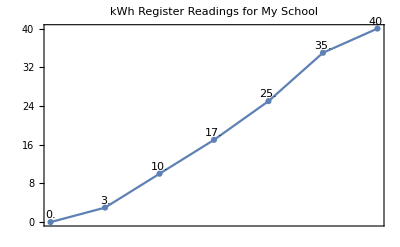

```mathematica
DateListPlot[
TimeSeries[Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotLabel->"kWh Register Readings for My School",
PlotTheme->"Detailed"]
```

To deploy the chart so that it can be viewed through a browser you use the CloudDeploy function with the same code used above.  By including the Delayed function, we ensure that the plot evaluates  when someone accesses the deployed expression.  This ensures that when the expression is accessed following the addition of register readings to the CloudExpression it reflects the current data.  Without inclusion of Delayed the deployed expression will always reflect the state of the data at the time of deployment.

```mathematica
clouddeployedDateListPlot=CloudDeploy[Delayed[
DateListPlot[
TimeSeries[Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotLabel->"kWh Register Readings for My School",
PlotTheme->"Detailed"]]]
```

CloudObject[https://www.wolframcloud.com/obj/83a8ee9b-2741-4216-a198-3bc92415311b]

```mathematica
SetPermissions[%,"Public"]
```

Use DeleteObject to delete the CloudObject.  Within the same kernel session you can use the form used below.  In a different kernel session you will need to fully specify the CloudObject.

```mathematica
DeleteObject[clouddeployedDateListPlot]
```

## Chapter 2: Additional Data Types and Sources

## Introduction

In the first chapter we demonstrated how to build  simple components to track electrical energy consumption by recording register readings from the face of the meter.  In this chapter we will explore how to define components to track other data types, such as records of bulk deliveries of commodities such as fuel oil, or wood. 

We will also explore how to import historical data into the application from a spreadsheet.  If you engage with your school administrators you will probably find that someone at your school has a spreadsheet of monthly utility bills that goes back many years.  Importing data from a spreadsheet will enable you to quickly add your school’s historical energy consumption to your application.  

You may also find that your school’s utility company makes historical bills, or even much finer grained data, available for download from their website.  Take some time to explore the website of your utility company, and keep an eye open for the “Green Button”.  The Green Button Initiative defined a standard data format that many utilities use to enable their customers to download their data.

```mathematica
WebImageSearch["Green Button Initiative","Images",MaxItems->3]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WebSearch["Green Button",MaxItems->5]
```

WebSearch::nval: Invalid value for parameter Language in service BingSearch.

Dataset[<>]

At the end of this chapter we will have all of the tools necessary to build an application that can track all of the fuel consumption of a single building.  In Chapter 3 we will pull everything together to deploy a working application.

## User Stories

### Plot Fuel Oil Deliveries Over Time

#### Story Details

As a participant in my school’s energy tracking initiative,  I want to plot my school’s fuel oil deliveries  over time.

#### Background Information

Some energy sources such as fuel oil, or wood, are delivered in large quantities, at irregular intervals, stored on site, and consumed over time.    Plots of the delivery of these commodities over time may benefit from  different presentation than plots of regular time series data due to the irregularity of the deliveries .  For instance, if you wish to create a monthly plot of fuel oil deliveries, you may find that some months have several deliveries, while some have none.  A continuous line plot depicting this type of data can make it difficult to discern when deliveries occur.

It is also worth remembering that the time of delivery and time of consumption are quite different.  In later sections we will examine ways of estimating the time of consumption from the operation time of boilers, or thermostat data that provides information about when fuel is being used.

#### Code Explanation

First, we create a list of time-value pairs that account for the deliveries to a single location over a year.

```mathematica
fueloildeliveries={{DateObject[{2019,1,10}],250},{DateObject[{2019,1,25}],200},{DateObject[{2019,3,5}],370},{DateObject[{2019,3,20}],250},{DateObject[{2019,5,1}],260},{DateObject[{2019,6,30}],150},{DateObject[{2019,8,30}],110},{DateObject[{2019,10,5}],200},{DateObject[{2019,11,15}],220},{DateObject[{2019,12,14}],270}};
```

Now we create a TimeSeries of the data and plot it.

```mathematica
fueloildeliveriesTimeSeries=TimeSeries[fueloildeliveries]
```

TimeSeries[…]

```mathematica
DateListPlot[fueloildeliveriesTimeSeries]
```

Since the data is irregular, it may be useful to regularize the data into monthly totals. The TimeSeriesAggregate function allows us to do that.

```mathematica
fueloildeliveriesTimeSeriesAggregate=TimeSeriesAggregate[TimeSeries[fueloildeliveriesTimeSeries],"Month",Total]
```

TimeSeries[…]

This plot has both the monthly aggregate, and individual delivery time series.

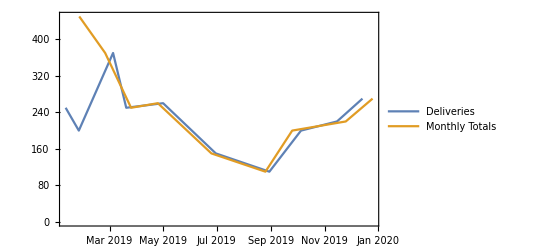

```mathematica
DateListPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},
PlotLegends->{"Deliveries","Monthly Totals"}]
```

An alternate presentation that clarifies each discrete time point is to use the DateListStepPlot.

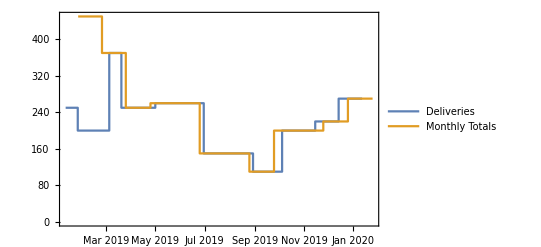

```mathematica
DateListStepPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},PlotLegends->{"Deliveries","Monthly Totals"}]
```

Setting Joined to False on a DateListPlot also clarifies the individual deliveries, and their spacing over time.

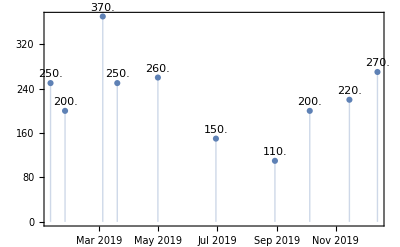

```mathematica
DateListPlot[fueloildeliveriesTimeSeries,
Filling->Axis,
Joined->False,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed"]
```

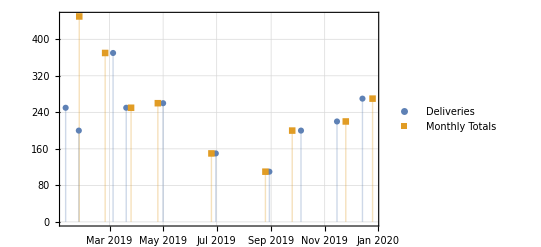

```mathematica
DateListPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},
Filling->Axis,
Joined->False,
PlotMarkers->Automatic,
PlotTheme->"Detailed",
PlotLegends->{"Deliveries","Monthly Totals"}]
```

### Create a form for entering fuel oil deliveries that allows the user to specify the date.

#### Story Details

As a participant  in my school’s energy tracking initiative I want to be able to record fuel oil deliveries in a form, and specify the date that the delivery occurred.

#### Explanation

In Chapter 1 the forms for entering register readings  assumed the date was Yesterday or Today.  In this form we add a new field to specify the date.   The Wolfram Language Interpreter function allows you to specify a wide variety of ways of interpreting a form’s fields.  In this case, we specify that the form be interpreted as a “Date”, which according to the documentation will accept “any standard format or in natural language”.  A “Hint” is added, which suggests the format that the user should enter, although it does not actually restrict the format.

#### Code Explanation

```mathematica
DeleteCloudExpression["fueloildeliveriesCloudExpression"]
```

First, we create a CloudExpression to hold the fuel oil deliveries.

```mathematica
fueloildeliveriesCloudExpression=CreateCloudExpression[fueloildeliveries,"fueloildeliveriesCloudExpression"]
```

CloudExpression[…]

The first Argument of FormPage creates a Date field that will interpret the entered value as a Date.  Try entering Dates in different formats within the Date field to test the flexibility of the Date Interpreter.  This form will add records of fuel oil deliveries to the CloudExpression from the prior story.

```mathematica
fuelOilFormPage=FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"Gallons"->"Integer"},
AppendTo[CloudExpression["fueloildeliveriesCloudExpression"],{#Date,#Gallons}]&,
AppearanceRules-><|"Title"->"Enter a fuel oil delivery",
"Description"->"Enter a date and the number of gallons delivered"|>]
```

As you enter new values in the form, evaluate the DateListPlot below to see if the form successfully added a record to the CloudExpression.

```mathematica
DateListPlot[TimeSeries[
Get[CloudExpression["fueloildeliveriesCloudExpression"]]],
Filling->Axis,
Joined->False,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed"]
```

-Graphics-

### Import Monthly Bills from a Spreadsheet to a CloudExpression

#### Story Details

-As a participant in my school’s energy tracking initiative I want to be able to import the school’s monthly bill data stored in a spreadsheet into a CloudExpression so that the data can be used by an application, or user with access to the CloudExpression.

#### Background Information

It is likely that someone in your school keeps a spreadsheet with years of utility bill data.  If you can access that spreadsheet, the data in it can be imported into the Wolfram Language and stored in a CloudExpression with a few lines of code.

#### Code Explanation

In this story we will briefly touch upon additional data structures within the Wolfram Language.  In the first chapter we worked with lists of date-value pairs.  We still want to store the data as lists of date-value pairs, but the data will be imported into a Dataset structure, transformed into a structure that uses Associations, and is finally transformed to the list of date-value pairs that we will store in the cloud expression.

Dataset is similar to a typical table structure in a relational database, or even a spreadsheet.  The imported Dataset has columns with column Headers that define the data. The SemanticImport function will import data in a spreadsheet or similar file format, and return a Dataset object.

```mathematica
monthlyBillDataset=SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Monthly_Bills.csv"]
```

Dataset[<>]

The use of Normal in the code below transforms the Dataset to a list of pairs of Associations.

```mathematica
normalmonthlyBillDataset=Normal[monthlyBillDataset]
```

{<|Bill Date→Day: Mon 20 Nov 2017,KWH→1091|>,<|Bill Date→Day: Wed 20 Dec 2017,KWH→941|>,<|Bill Date→Day: Fri 19 Jan 2018,KWH→1258|>,<|Bill Date→Day: Wed 21 Feb 2018,KWH→1134|>,<|Bill Date→Day: Thu 22 Mar 2018,KWH→1036|>,<|Bill Date→Day: Fri 20 Apr 2018,KWH→904|>,<|Bill Date→Day: Tue 22 May 2018,KWH→1045|>,<|Bill Date→Day: Thu 21 Jun 2018,KWH→807|>,<|Bill Date→Day: Tue 24 Jul 2018,KWH→788|>,<|Bill Date→Day: Wed 22 Aug 2018,KWH→482|>,<|Bill Date→Day: Fri 21 Sep 2018,KWH→630|>,<|Bill Date→Day: Mon 22 Oct 2018,KWH→886|>,<|Bill Date→Day: Wed 21 Nov 2018,KWH→744|>,<|Bill Date→Day: Thu 20 Dec 2018,KWH→714|>,<|Bill Date→Day: Mon 21 Jan 2019,KWH→847|>,<|Bill Date→Day: Wed 20 Feb 2019,KWH→729|>,<|Bill Date→Day: Thu 21 Mar 2019,KWH→688|>,<|Bill Date→Day: Mon 22 Apr 2019,KWH→626|>,<|Bill Date→Day: Tue 21 May 2019,KWH→776|>,<|Bill Date→Day: Thu 20 Jun 2019,KWH→1044|>,<|Bill Date→Day: Mon 22 Jul 2019,KWH→1010|>,<|Bill Date→Day: Wed 21 Aug 2019,KWH→961|>,<|Bill Date→Day: Fri 20 Sep 2019,KWH→914|>,<|Bill Date→Day: Mon 21 Oct 2019,KWH→900|>}

The Map function, applies a function to each entry in a list.  In this case the code below takes each pair of associations, and creates a list of pairs of  Bill Date and KWH values.  This is the form that we save in the CloudExpression.

```mathematica
listofMonthlyBills=Map[
		{#["Bill Date"], #["KWH"]} &,
		normalmonthlyBillDataset]
```

{{Day: Mon 20 Nov 2017,1091},{Day: Wed 20 Dec 2017,941},{Day: Fri 19 Jan 2018,1258},{Day: Wed 21 Feb 2018,1134},{Day: Thu 22 Mar 2018,1036},{Day: Fri 20 Apr 2018,904},{Day: Tue 22 May 2018,1045},{Day: Thu 21 Jun 2018,807},{Day: Tue 24 Jul 2018,788},{Day: Wed 22 Aug 2018,482},{Day: Fri 21 Sep 2018,630},{Day: Mon 22 Oct 2018,886},{Day: Wed 21 Nov 2018,744},{Day: Thu 20 Dec 2018,714},{Day: Mon 21 Jan 2019,847},{Day: Wed 20 Feb 2019,729},{Day: Thu 21 Mar 2019,688},{Day: Mon 22 Apr 2019,626},{Day: Tue 21 May 2019,776},{Day: Thu 20 Jun 2019,1044},{Day: Mon 22 Jul 2019,1010},{Day: Wed 21 Aug 2019,961},{Day: Fri 20 Sep 2019,914},{Day: Mon 21 Oct 2019,900}}

```mathematica
CreateCloudExpression[listofMonthlyBills,"listofMonthlyBills"]
```

CloudExpression[…]

```mathematica
DeleteCloudExpression["listofMonthlyBills"]
```

Now we can retrieve the values from the CloudExpression, and plot them.

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["listofMonthlyBills"]]]]
```

Now we can tie the set of functions above into a single operation that we could could use on other spreadsheets.

```mathematica
CreateCloudExpression[
Map[{#["Bill Date"], #["KWH"]} &,Normal[SemanticImport["enter file path"]]],"Monthly Bills"]
```

### Import Interval Data from a Spreadsheet into a New CloudExpression

#### Story Details

As a participant in my School’s energy tracking initiative I want to be able to  import the interval data that is in a spreadsheet into a new CloudExpression so that the data can be stored in a central location and shared so that other users or applications can view or analyze the data.

#### Background Information

Modern electrical meters, often referred to as “smart meters” are capable of recording and reporting energy consumption within relatively short intervals.  Many utilities now program their meters to record intervals of 15 , 30 or 60 minutes.  Many meters are capable of recording intervals as short as 1 minute, but the cost of processing and storing the volume of data resulting from 1 minute intervals is considerable.  

Interval data provides significant insight into how a building uses energy.  You can see when a building uses energy during the day, and infer what the major consumers are at different points of the day.

#### Code Explanation

One can use the same code to import interval data as we used to import monthly bill data.  The primary difference here is that the column headers on the imported file are different, and we name this CloudExpression “Interval Data”.

```mathematica
DeleteCloudExpression["Interval Data"]
```

```mathematica
CreateCloudExpression[
Map[{#["IntervalEnd"], #["Quantity"]} &,Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Interval_September.csv"]]],"Interval Data"]
```

CloudExpression[…]

Here we plot the interval data.  Notice the density of the data points.  A meter recording 15 minute interval data generates 96 data points in a day if it is measuring a single time series.  This is 2880 data points in a month compared to the single data point  that was available in the era of manually collected meter readings.

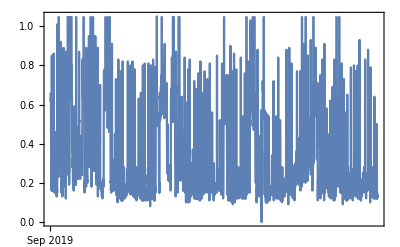

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

### Add Interval Data from a Spreadsheet to an Existing CloudExpression

#### Story Details

As a participant in my school’s energy tracking initiative I want to be able to upload interval readings in a spreadsheet to an existing CloudExpression that contains additional interval data.

#### Background Information

In the first story uploading interval data to a CloudExpression we created the CloudExpression, and uploaded a complete list of time-value pairs within the same function.  We require different code to add incremental data to an existing CloudExpression.

#### Code Explanation

First, we will use our code to create a list of time-value pairs of the incremental data that we wish to add.  The spreadsheet used here contains data for the month following the data imported in the prior user story.

```mathematica
incrementalIntervalData=Map[{#["IntervalEnd"], #["Quantity"]} &,Normal[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Sample Data\\Sample_Interval_October.csv"]]]
```

{{Tue 1 Oct 2019 00:15:00GMT-5.,0.13},{Tue 1 Oct 2019 00:30:00GMT-5.,0.13},{Tue 1 Oct 2019 00:45:00GMT-5.,0.15},{Tue 1 Oct 2019 01:00:00GMT-5.,0.11},{Tue 1 Oct 2019 01:15:00GMT-5.,0.17},{Tue 1 Oct 2019 01:30:00GMT-5.,0.15},{Tue 1 Oct 2019 01:45:00GMT-5.,0.14},2867,{Wed 30 Oct 2019 22:45:00GMT-5.,0.82},{Wed 30 Oct 2019 23:00:00GMT-5.,0.71},{Wed 30 Oct 2019 23:15:00GMT-5.,0.64},{Wed 30 Oct 2019 23:30:00GMT-5.,0.66},{Wed 30 Oct 2019 23:45:00GMT-5.,0.62},{Thu 31 Oct 2019 00:00:00GMT-5.,0.64}}
 |  |  |  |

Where we used AppendTo to add new register readings to an existing CloudExpression in the first chapter, that function would be very inefficient in the context of adding thousands of new records to a CloudExpression, as AppendTo returns an updated CloudExpression with each incremental value. This code uses the Put function to fully replace the existing content of CloudExpression “Interval Data” with completely new content.  The new content is a union of the existing data within the CloudExpression and the incrementalIntervalData.

```mathematica
Put[Union[Get[CloudExpression["Interval Data"]],
incrementalIntervalData],
CloudExpression["Interval Data"]]
```

CloudExpression[…]

We can now visualize the CloudExpression to see an additional month of data has been added.

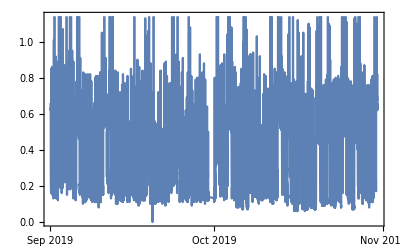

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

The code below ties it all together.

```mathematica
Put[Union[Get[CloudExpression["Interval Data"]],
Map[{#["IntervalEnd"], #["Quantity"]} &,
Normal[SemanticImport["C:\\Users\\kylem\\OneDrive\\Holderness Project\\Computational Sustainability Toolkit\\Sample_Interval_October.csv"]]]],
CloudExpression["Interval Data"]]
```

### Not Complete- Use a Form to Add Interval Data from a Spreadsheet to an existing CloudExpression

#### Story Details

As a participant in my school’s energy tracking initiative I want to be able to upload interval data from a CSV file to an existing CloudExpression through a web form.

To date I can’t get the form, either cloud deployed or locally to work.

#### Code Explanation

This code takes our function that appends interval data to an existing CloudExpression and places it in a FormPage.  The inputs to the page are a CSV file, and the name of the CloudExpression.

```mathematica
intervalDataForm=FormPage[
{"CSV"->"CSV",{"ExpressionName","Expression Name"}->"String"},
Put[Union[Get[CloudExpression[#ExpressionName]],
Map[{#["IntervalEnd"], #["Quantity"]}&,
Normal[SemanticImport[#CSV]]]],
CloudExpression[#ExpressionName]]&,
AppearanceRules-><|"Title"->"Upload a CSV with interval data",
"Description"->"Select a CSV file and provide Cloud Expression name.  The CSV should have columns with headers named IntervalEnd and Quantity."|>]
```

When the form is defined we can CloudDeploy it so that anyone with permission can use it to upload data.

```mathematica
CloudDeploy[intervalDataForm]
```

We can plot the data again to see that additional data has been added.

```mathematica
Get[CloudExpression["Interval Data"]]
```

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

-Graphics-

### Specify the window of interval data displayed in a DateListPlot

#### Story Details

-As a participant in my school’s energy tracking initiative trying to understand how my school consumes electricity, I want to be able to specify the time window of interval data displayed in a DateListPlot or similar visualization.

#### Background Information

In this story we introduce Manipulate, which is a primary function through which users of the system can manipulate the variables of an expression.  Manipulate

#### Code Explanation

To simplify our code later, first we will define a local TimeSeries object with our CloudExpression data.

```mathematica
intervaldataTimeSeries=TimeSeries[Get[CloudExpression["Interval Data"]]]
```

TimeSeries[…]

If you want to plot only a portion of a TimeSeries, instead of a complete TimeSeries, you apply the TimeSeriesWindow function to a TimeSeries object.  The first argument of the TimeSeriesWindow is the TimeSeries, and the second and third arguments (or perhaps second) are the first time and last time of the window that you wish to select.  First we will plot the complete TimeSeries.

```mathematica
DateListPlot[intervaldataTimeSeries]
```

-Graphics-

Here we will use TimeSeriesWindow to visualize a full day of interval data.

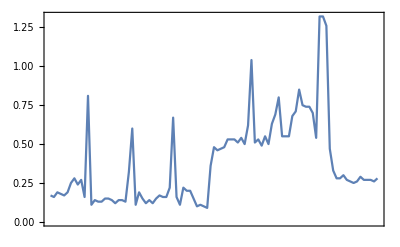

```mathematica
DateListPlot[TimeSeriesWindow[intervaldataTimeSeries,{DateObject[{2019,10,14,0,0}],DateObject[{2019,10,15,0,0}]}]]
```

That works, but we don’t really want to make people type in a date every time they want to select a different window.  We can make the user’s life easier by integrating Manipulate into the expression.  Manipulate is the primary function that allows users to interact with data on the screen.  The manipulate function allows you to manipulate multiple variables within an expression.  In this case we will allow the user to manipulate both the lower bound, and the upper bound of the TimeSeriesWindow.  To do this, we will take advantage of the TimeSeries properties “FirstTime” and “LastTime”.

To retrieve a property of a TimeSeries you can use the following form.

```mathematica
intervaldataTimeSeries["FirstTime"]
```

3776285700

This output is UnixTime, which is precise, but not exactly meaningful.  To see a human readable value we can wrap that in a DateObject.

```mathematica
DateObject[intervaldataTimeSeries["FirstTime"]]
```

Sun 1 Sep 2019 00:15:00GMT-5.

In a Manipulate expression you specify the variables within the expression that you wish to manipulate, and then you define the parameters for each variable individually.  In this case “a” and “b” define the window of the TimeSeriesWindow function.  The syntax used here to define each variable is {{variable, default value, “label”}, the lower bound of the window, and the upper bound of the window}. Note that the default value, and the lower and upper bounds of the window are defined as the “FirstTime” and “LastTime” of the TimeSeries being visualized.  This ensures that the complete TimeSeries can be viewed, and prevents selection of dates outside of the TimeSeries.

```mathematica
Manipulate[DateListPlot[
TimeSeriesWindow[intervaldataTimeSeries,{a,b}]],
{{a,intervaldataTimeSeries["FirstTime"],"Start Date"},intervaldataTimeSeries["FirstTime"],intervaldataTimeSeries["LastTime"]},{{b,intervaldataTimeSeries["LastTime"],"End Date"},intervaldataTimeSeries["FirstTime"],intervaldataTimeSeries["LastTime"]}]
```

Here we will define our first Function.  Functions allow you to simplify the task of using code that you will use repeatedly.  In the expression below we name the function manipulateDateListPlotTimeSeries, and name the argument timeseries_.  The code of the function is identical to the code above, but “timeseries” is used in every instance within the function that a specific TimeSeries would be specified.  After you evaluate the Function, you can use it with any TimeSeries as the argument.

```mathematica
manipulateDateListPlotTimeSeries[timeseries_]:=Manipulate[DateListPlot[
TimeSeriesWindow[timeseries,{a,b}]],
{{a,timeseries["FirstTime"],"Start Date"},timeseries["FirstTime"],timeseries["LastTime"]},
{{b,timeseries["LastTime"],"End Date"},timeseries["FirstTime"],timeseries["LastTime"]}]
```

```mathematica
manipulateDateListPlotTimeSeries[intervaldataTimeSeries]
```

```mathematica
manipulateDateListPlotTimeSeries[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

```mathematica
CloudDeploy[Delayed[
manipulateDateListPlotTimeSeries[Get[CloudExpression["Interval Data"]]]]]
```

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/obj/b3f01761-a460-4540-be31-f76123eed2c9"]]
```

## Chapter 3: Building and Deploying the Application

## Introduction

In this chapter we will take the building blocks of Forms, CloudExpressions, DateList plots, and Permissions that we learned in the prior chapters to build a simple application that will enable your energy tracking initiative to continue to add data through a form after the original data collection is complete, to publish it’s energy consumption data, and manage permissions to control access to the forms and published data.

## User Stories

### Administrator manages deployments through a project notebook

#### Story Details

As the administrator of my school’s energy tracking initiative I would like to be able to manage the deployment of project artifacts through a single interface.

#### Background Information

There is no new code that is part of this user story. Rather, there is a single notebook that contains all of the code necessary to create and deploy the artifacts necessary for an energy tracking initiative to track the energy consumed by a single building. That notebook is titled "School Energy Tracking Project Notebook", and can be found in the Code Samples folder of the GitHub repository.  you can use that notebook as is, or modify it as you wish.

The subsequent user stories in this chapter will have code samples for reference.  The relevant code can also be found within the Project Notebook.

### Administrators manage deployments through a shared project notebook

#### Story Details

As the administrators of my school’s energy tracking initiative we would all like to be able to access the project notebook.

#### Code Explanation

The CloudShare function allows multiple users to share access to a notebook through their WolframCloud accounts.  It is analogous to shared documents in any cloud document management system where multiple users are able to access the same document.  The code below shares the notebook in which the function is being evaluated (this is what EvaluationNotebook[] does) with the members of the PermissionsGroup “administrator”.

```mathematica
CloudShare[EvaluationNotebook[],PermissionsGroup["administrator"]]
```

### Administrator manages user access to deployed CloudObjects and CloudExpressions

#### Story Details

As  an administrator of my school’s energy tracking initiative I would like to be able to control which individuals have access to the forms that add new data to cloud expressions, and to the project notebook.  I would like different individuals to have access to the forms than to the project notebook.

#### Background Information

The Wolfram Language provides native capabilities for managing permissions to CloudObjects, CloudExpressions and CloudShared notebooks through PermissionsGroups.  This enables assigning a single user permissions to multiple CloudObjects by assigning them to a single PermissionsGroup that provides permissions to those CloudObjects.  For a detailed explanation of the functionality see the Wolfram documentation “Create and Maintain a Permissions Group”.

#### Code Explanation

This creates a PermissionsGroup. The email addresses assigned to the group must be active Wolfram IDs.  Anyone can create a free Wolfram ID here.  Note that $CloudUserID assigns the user creating the group to the group.  This first function creates an “administrator” PermissionsGroup with a single user.

```mathematica
CreatePermissionsGroup["administrator",{$CloudUserID}]
```

This next piece of code is what you should use to manage the users of the group after the group’s original creation.  Every time you use the SetUsers function the list of users replaces the prior list of users.  You can also use the AddUsers and RemoveUsers to incrementally add or remove users from the list.

```mathematica
SetUsers["administrator",{"administrator1@myschool.edu","administrator2@myschool.edu"}]
```

This code assigns the “administrator” group to a CloudExpression.  In this case, it is the form

```mathematica
SetPermissions[CloudExpression["registerReadingsCloudExpression"],PermissionsGroup["administrator"]->{"Read","Write","Execute"}]
```

### Member of the public accesses all energy tracking visualizations through a single entry point.

#### Story Details

As a school’s energy tracking initiative we want to provide a single entry point to members of the public and initiative participants to the visualizations of all of our school’s energy consumption data, as well as the forms used to add additional data.

#### Code Explanation

There are several ways to  publish materials using the Wolfram Language, and several ways that we could tie all of our forms and visualizations together.  For now we will use a relatively simple method which is to CloudPublish a notebook that has hyperlinks to the individual visualizations and forms.  

Please see the “School Energy Consumption Page” notebook in the Code Samples directory of the GitHub repository.  What you will find in that notebook is quite simple.  Each visualization and form page has a hyperlink to it within the notebook.  You can add much more content to your notebook if you wish.

The code below CloudPublishes the “School Energy Consumption Page” notebook.  To CloudPublish a notebook you need to include a NotebookObject in the function.  One way to acquire the NotebookObject  is to evaluate EvaluationNotebook[] within the notebook that you intend to publish. I simply copy the returned NotebookObject, and paste it into the CloudPublish function.  Before you CloudPublish the notebook delete the EvaluationNotebook code.    Note that CloudPublish makes the notebook available to the public.

The example notebook has hyperlinks to example forms and visualizations.  You will want to introduce hyperlinks to your own forms and visualizations into the notebook.

```mathematica
CloudPublish[bxwvw_shm23FrontEndObject[LinkObject["bxwvw_shm", 3, 1]]23"School Energy Consumption Page.nb""C:\\Users\\kylem\\Documents\\GitHub\\Computational-Sustainability-Toolkit\\Code Samples\\School Energy Consumption Page.nb","MySchoolNotebook"]
```

Since the CloudPublished notebook is distinct from the individual visualizations and forms that the notebook links to the permissions to the visualizations and forms need to be managed independently.  The next story will cover how to do this.

Copyright 2020 Kyle MacLaury

Licensed under the Apache License, Version 2.0 (the "License");
you may not use this file except in compliance with the License.You may obtain a copy of the License at

http : // www.apache.org/licenses/LICENSE - 2.0

Unless required by applicable law or agreed to in writing, software
distributed under the License is distributed on an "AS IS" BASIS, WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.See the License for the specific language governing permissions and
limitations under the License.